# Magnonic thermal conductivity on a square lattice with Dzyaloshinskii-Moriya interaction

```mathematica
d=-1;
z=6;
γ[kx_,ky_]:=2*(Cos[kx]+Cos[ky]);
ϵ[kx_,ky_,kz_,b_]:=4d*Sqrt[z^2+z*γ[kx,ky]];
heatconductivitydensityempiric[kx_,ky_,kz_,b_,β_,ξ_]:=-(4^4*d^4*z^2 *(Sin[kx]^2+Sin[ky]^2+Sin[kz]^2))*(β^2/2)/(1-Cosh[β*ϵ[kx,ky,kz,b]])*(1)/(2*ξ[##])&;
ξac[kx_,ky_,kz_,β_,b_]:=Sqrt[kx^2+ky^2+kz^2]/(β^2*16*Sqrt[2]);
ξmm[kx_,ky_,kz_,β_,b_]:=Sqrt[kx^2+ky^2+kz^2]*Exp[-2.2*d*β];
ξgb[kx_,ky_,β_,b_]:=16*Sqrt[2]/150;
ξcor[kx_,ky_,β_,b_]:=16*Sqrt[2]/(1.13*d*Exp[1.13*d*β]/(2.26*d+1/β));
ξcomb[kx_,ky_,kz_,β_,b_]:=16*Sqrt[2]/150+Sqrt[kx^2+ky^2]/(β^2*16*Sqrt[2]);
```

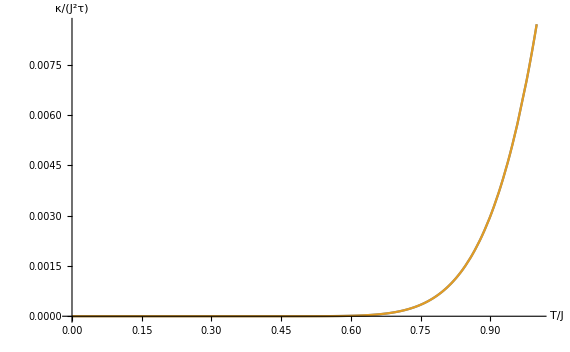

```mathematica
Plot[{1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,kz,0,1/T,ξcomb][kx,ky,kz,1/T,0],{kx,-π,π},{ky,-π,π},{kz,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,kz,1,1/T,ξcomb][kx,ky,kz,1/T,1],{kx,-π,π},{ky,-π,π},{kz,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0,1},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```